A(τ) as a Gamma(2, 1/2) distribution (noting Mathematica uses scale instead of rate):

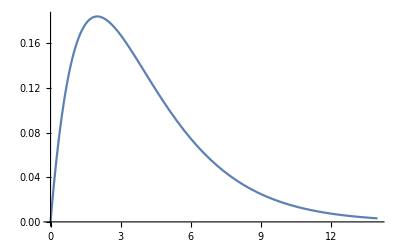

```mathematica
Plot[PDF[GammaDistribution[2,2],x],{x,0,14}]
```

Stepwise a_i(τ):

```mathematica
n = 20;
latentdraws = RandomVariate[ExponentialDistribution[1/2], n];
infectiousdraws = RandomVariate[ExponentialDistribution[1/2], n];
```

```mathematica
pwgen[latent_, infectious_]:=Piecewise[
{{0, x≤latent},
{0.15 + 0.002*RandomReal[1], x>latent && x≤ latent+infectious},
{0, x>latent+infectious}}
]
```

```mathematica
steps = pwgen[#[[1]], #[[2]]]&/@({latentdraws, infectiousdraws}ᵀ);
```

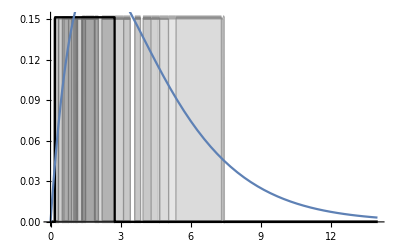

```mathematica
Show[Plot[steps,{x,0,14}, PlotStyle->{{Gray, Opacity[0.6]}}, ExclusionsStyle->{{Gray, Opacity[0.6]}}, Filling->Axis, FillingStyle->{Gray, Opacity[0.1]}],
Plot[steps[[1]],{x,0,14}, PlotStyle->{{Black, Opacity[1]}}, ExclusionsStyle->{{Black, Opacity[1]}}, Filling->Axis, FillingStyle->{Gray, Opacity[0.1]}],
Plot[PDF[GammaDistribution[2,2],x],{x,0,14}]]
```

Smooth :

```mathematica
Plot[PDF[GammaDistribution[2,2],x],{x,0,14}]
```

-Graphics-

Spike a_i(τ):

```mathematica
spikedraws = RandomVariate[GammaDistribution[2,2],20]
```

{0.728998,6.85122,2.28323,2.98182,11.8121,3.29007,5.48155,5.02068,2.70662,1.02284,2.54043,0.786993,1.84881,2.63697,6.5263,0.665412,2.16305,3.67373,5.71042,2.80465}

```mathematica
makearrows[xval_]:=Arrow[{{xval, 0},{xval, 0.15}}]
```

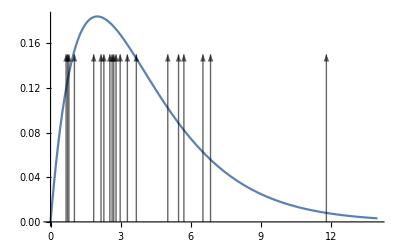

```mathematica
Show[Plot[PDF[GammaDistribution[2,2],x],{x,0,14}],
Graphics[{Black, Opacity[0.6], makearrows[#]&/@spikedraws}]]
```

```mathematica
β = 1;
γ = 1/2;
α = 1/3;
n=3;
A[τ_]:=β γ/(γ - α)(Exp[-α τ] - Exp[-γ τ]);
```

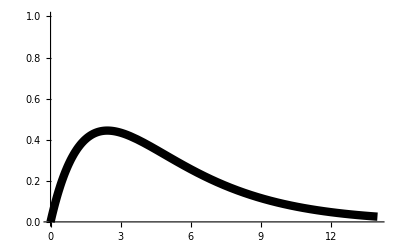

```mathematica
Plot[A[τ],{τ,0,14}, PlotRange->{0, β}, PlotStyle->{{Black,Thickness[0.015]}}]
```

```mathematica
(*2, 18, 19, 23, 36!*)
```

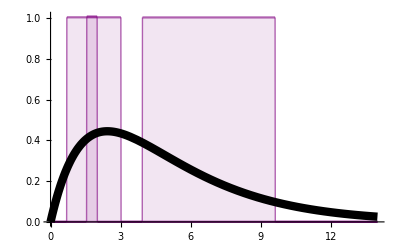

```mathematica
SeedRandom[36];
latentdraws = RandomVariate[ExponentialDistribution[γ], n];
infectiousdraws = RandomVariate[ExponentialDistribution[α], n];
pwgen[latent_, infectious_]:=Piecewise[
{{0, x≤latent},
{β+ β/100*RandomReal[1], x>latent && x≤ latent+infectious},
{0, x>latent+infectious}}
]
steps = pwgen[#[[1]], #[[2]]]&/@({latentdraws, infectiousdraws}ᵀ);
Show[
Plot[steps,{x,0,14}, PlotStyle->{{Purple, Opacity[0.6]}}, ExclusionsStyle->{{Purple, Opacity[0.6]}}, Filling->Axis, FillingStyle->{Purple, Opacity[0.1]}],
(*Plot[steps[[1]],{x,0,14}, PlotStyle->{{Black, Opacity[1]}}, ExclusionsStyle->{{Black, Opacity[1]}}, Filling->Axis, FillingStyle->{Gray, Opacity[0.1]}],*)
Plot[A[τ],{τ,0,14}, PlotStyle->{{Black,Thickness[0.015]}}]]
```

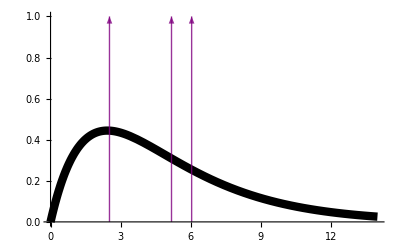

```mathematica
SeedRandom[2];
spikedraws = RandomVariate[ExponentialDistribution[γ],n] + RandomVariate[ExponentialDistribution[α],n];
makearrows[xval_]:=Arrow[{{xval, 0},{xval, β}}]
Show[Plot[A[τ],{τ,0,14}, PlotRange->{0,β}, PlotStyle->{{Black,Thickness[0.015]}}],
Graphics[{Purple, Opacity[0.8], makearrows[#]&/@spikedraws}]]
```

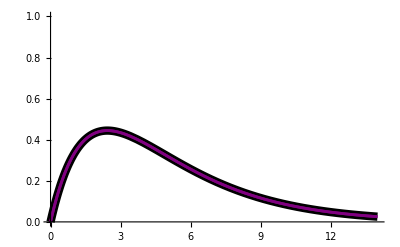

```mathematica
Show[Plot[A[τ],{τ,0,14}, PlotRange->{0,β}, PlotStyle->{{Black,Thickness[0.015]}}],
Plot[A[τ],{τ,0,14}, PlotRange->{0,β}, PlotStyle->{{Purple,Thickness[0.005]}}],
Plot[A[τ],{τ,0,14}, PlotRange->{0,β}, PlotStyle->{{Purple,Thickness[0.005]}}]]
```